```mathematica
F[t_]=mu (Ap Exp[-Abs[t]/taup]+Ad Exp[-Abs[t]/taud])
```

(Ad ⅇ^(-Abs[t]/taud)+Ap ⅇ^(-Abs[t]/taup)) mu

```mathematica
SubsExpl={mu->1,Ap->8/100,Ad->-533/10000,taup->25/1000,taud->5/100,taus->1/100};
Asspt={taup>0,taud>0,mu>0,Ap>0,Ad<0,w∈Reals,taus>0,alpha∈Integers,beta∈Integers, k∈ Integers,k≥0};
```

```mathematica
Ftilde[w_]=2mu (Ap taup/(1+taup^2 w^2)+Ad taud/(1+taud^2 w^2))
```

2 mu ((Ad taud)/(1+taud^2 w^2)+(Ap taup)/(1+taup^2 w^2))

```mathematica
atilde[w_]=1/(1+I w taus)
```

1/(1+ⅈ taus w)

```mathematica
palpha[alpha_,t_]=1/((alpha-1)!taus^alpha)t^(alpha-1)Exp[-t/taus]UnitStep[t]
```

(ⅇ^(-t/taus) t^(-1+alpha) taus^-alpha UnitStep[t])/((-1+alpha)!)

```mathematica
p[alpha_,beta_,Dt_]:=Integrate[palpha[alpha,Dt-talpha]*palpha[beta,-talpha],{talpha,-∞,∞},Assumptions->Join[Asspt,{Dt∈Reals}]]
```

```mathematica
For[kExpl=5,kExpl<=20,kExpl+=15,
pk[kExpl,0,Dt_]=palpha[kExpl,-Dt];
pk[kExpl,kExpl,Dt_]=palpha[kExpl,Dt];
For[alphaExpl=1,alphaExpl≤kExpl-1,alphaExpl++,
pk[kExpl,alphaExpl,Dt_]=Simplify[p[alphaExpl,kExpl-alphaExpl,Dt]];
];
]
```

```mathematica
For[kExpl=5,kExpl≤20,kExpl+=15,
For[alphaExpl=0,alphaExpl≤kExpl,alphaExpl++,
pkExpl[kExpl,alphaExpl,Dt_]=pk[kExpl,alphaExpl,Dt]/.SubsExpl;
];
]
```

```mathematica
PlotLims=0.5;
```

0.5

```mathematica
P0=Plot[{pkExpl[5,0,Dt]/.Dt->SetAccuracy[t,100],pkExpl[5,1,Dt]/.Dt->SetAccuracy[t,100],pkExpl[5,2,Dt]/.Dt->SetAccuracy[t,100],pkExpl[5,3,Dt]/.Dt->SetAccuracy[t,100],pkExpl[5,4,Dt]/.Dt->SetAccuracy[t,100],pkExpl[5,5,Dt]/.Dt->SetAccuracy[t,100]},{t,-PlotLims,PlotLims},PlotRange->{{-0.5,0.5},{0,22}},PlotStyle->ColorData[97,2]];
```

```mathematica
P1=Plot[{pkExpl[20,0,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,1,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,2,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,3,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,4,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,5,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,6,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,7,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,8,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,9,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,10,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,11,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,12,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,13,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,14,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,15,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,16,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,17,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,18,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,19,Dt]/.Dt->SetAccuracy[t,100],pkExpl[20,20,Dt]/.Dt->SetAccuracy[t,100]},{t,-PlotLims,PlotLims},PlotRange->{{-0.5,0.5},{0,22}},PlotStyle->ColorData[97,4]];
```

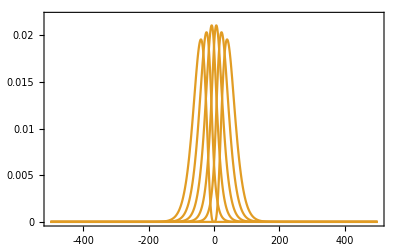

```mathematica
Show[P0, BaseStyle ->{FontFamily ->  "Times",FontSize -> 20},AxesStyle->{White,Opacity[0]},TicksStyle -> {Opacity[1],24},Frame ->{True},FrameStyle -> Thick,FrameTicks->{    { { {0,0},{5,0.005},{10,0.010},{15,0.015},{20,0.020}  }  ,None  }   ,  { { {-0.4,-400},{-0.2,-200},{0.,0},{0.2,200},{0.4,400}  }  ,None  } }    ,FrameTicksStyle->Black]
```

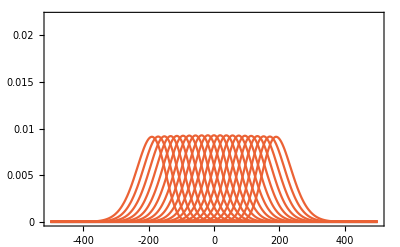

```mathematica
Show[P1, BaseStyle ->{FontFamily ->  "Times",FontSize -> 20},AxesStyle->{White,Opacity[0]},TicksStyle -> {Opacity[1],24},Frame ->{True},FrameStyle -> Thick,FrameTicks->{    { { {0,0},{5,0.005},{10,0.010},{15,0.015},{20,0.020}  }  ,None  }   ,  { { {-0.4,-400},{-0.2,-200},{0.,0},{0.2,200},{0.4,400}  }  ,None  } }    ,FrameTicksStyle->Black]
```